# Vaje za 5. teden

20. 3. 2025

## Naloga 1

Napiši funkcijo odvodPolinoma, ki kot argument sprejme polinom v splošni obliki in vrne njegov odvod. Pri tem uporabi le prepisovalna pravila. S pomočjo te funkcije odvajaj polinom x^2 + 3x + 4.

```mathematica
prep = {x^y_ -> y x^(y-1), x-> 1};
odvodPolinoma[p_] := (p /. prep) - (p /. {x -> 0});
odvodPolinoma[x^2 + 3x + 4]
```

3+2 x

## Naloga 2 - rešite 3. kolokvij iz matematike

-Graphics-

```mathematica
ClearAll[a, f, x, b]
f[x_] := Piecewise[{
{ArcTan[1/(x*x - 1)], x > 1}, 
{a, x == 1},
{(b Sin[x- 1])/ (x * x - 1), x < 1}
}]

limita1 = Limit[f[x], x -> 1, Direction->"FromAbove"]
```

π/2

```mathematica
limita2 = a
```

a

```mathematica
limita3 = Limit[f[x], x -> 1, Direction->"FromBelow"]
```

b/2

```mathematica
Solve[{limita1 == limita2 == limita3}]
```

{{a→π/2,b→π}}

-Graphics-

```mathematica
(* k tangente *)
ClearAll[x, f,a, g]
f[x_] := Sqrt[x * x + 1]
```

```mathematica
df= D[f[x], x];
kTangente = df /. {x -> 1}; (* v točki T*)
kNormale = - 1 / kTangente;
normalaT[x_] := kNormale * (x - 1) + f[1];
g[x_] := a - x*x;
```

```mathematica
dg = D[g[x], x];
xDotikalisca  = (Solve[dg == kNormale][[1]] // Values)[[1]]
```

1/(√2)

```mathematica
yg = g[xDotikalisca]
```

-1/2+a

```mathematica
normalaT[xDotikalisca]
```

√2-√2 (-1+1/(√2))

```mathematica
aR = (Solve[yg == normalaT[xDotikalisca], {a}][[1]] // Values)[[1]]
```

1/2 (-1+4 √2)

```mathematica
gg[x_] := g[x] /. {a -> aR}
```

```mathematica
Plot[{f[x], gg[x] , normalaT[x]}, {x, 0, 1.1}, PlotLabels->Automatic, AspectRatio->Automatic]
```

-Graphics-

-Graphics-

```mathematica
b[a_] := (l - a)/2
```

```mathematica
S[a_ ] := 1/2 * a * Sqrt[Power[b[a], 2] - Power[a, 2]/4]
dS = D[S[a], a]
```

(a (-a/2+(a-l)/2))/(4 √(-a^2/4+1/4 (-a+l)^2))+1/2 √(-a^2/4+1/4 (-a+l)^2)

```mathematica
Solve[dS == 0, {a}]
```

{{a→l/3}}

```mathematica
(* Enakostranični trikotnik s stranicami dolžine l/3 *)
```

-Graphics-

```mathematica
ClearAll[f, x]
```

```mathematica
f[x_] := (Log[x + 1])/(x+1)
```

```mathematica
(* definicijsko območje *)
FunctionDomain[f[x], x]
```

x>-1

```mathematica
(* Zaloga vrednosti *)
FunctionRange[f[x], x, y]
```

y≤1/ⅇ

```mathematica
(* Ničle *)
Reduce[f[x]==0, x]
```

x==0

```mathematica
(* Linearne asimptote *)
Limit[f[x], x-> Infinity]
```

0

```mathematica
(* Ekstremi *)
```

```mathematica
df = D[f[x], x];
Map[{#, f[#]}&, Solve[df == 0, x] // Flatten // Values]
```

{{-1+ⅇ,1/ⅇ}}

```mathematica
ddf = D[f[x], {x, 2}] ;
ddf /. {x -> -1 + E}
```

-1/ⅇ^3

```mathematica
(* V točki -1 + e je lokalni maksimum*)
```

```mathematica
(* Območja naraščanja *)
Reduce[df >= 0, x]
```

-1<x≤-1+ⅇ

```mathematica
(* Območja padanja *)
```

```mathematica
Reduce[df <= 0, x]
```

x≥-1+ⅇ

```mathematica
(* Prevoji *)
```

```mathematica
Reduce[ddf == 0, x]
```

x==-1+ⅇ^(3/2)

```mathematica
(* Konveksnost / konkavnost *)
Reduce[ddf >= 0, x] (* konveksno *)
Reduce[ddf <= 0, x] (* konkavno *)
```

x≥-1+ⅇ^(3/2)

-1<x≤-1+ⅇ^(3/2)

```mathematica
Plot[f[x], {x, -1, 4}, PlotLabels->Automatic]
```

-Graphics-

## Naloga 3

Funkcija f je podana s predpisom f(x) = ln((x^2-1)/2x). Določite definicijsko območje funkcije in ugotovite če je injektivna.

```mathematica
f[x_] := Log[(x^2-1)/2x]
```

```mathematica
FunctionDomain[f[x], x]
```

-1<x<0||x>1

```mathematica
Solve[f[x] == f[y], x] // FullSimplify
```

{{x→(2/3)^(1/3)/((-9 y+9 y^3+√3 √((-4+3 y^2) (-1+3 y^2)^2))^(1/3))+((9/2 y (-1+y^2)+√3 √(-1+27/4 y^2 (-1+y^2)^2))^(1/3))/3^(2/3)},{x→((-1)^(1/3) (-9 y+9 y^3+√3 √((-4+3 y^2) (-1+3 y^2)^2))^(1/3) ((-2)^(1/3)-(2 3^(1/3))/((-9 y+9 y^3+√3 √((-4+3 y^2) (-1+3 y^2)^2))^(2/3))))/6^(2/3)},{x→(2 (-3)^(2/3)-(-6)^(1/3) (-9 y+9 y^3+√3 √((-4+3 y^2) (-1+3 y^2)^2))^(2/3))/(6 (9/2 y (-1+y^2)+√3 √(-1+27/4 y^2 (-1+y^2)^2))^(1/3))}}

## Naloga 4

Izračunajte integral funkcije f(x, r) = ArcTan(r x) / (x (1 + x^2)) po spremenljivki x v odvisnosti od parametra r, kjer gre integral od nič do neskončno. Dobljeno preslikavo tudi poenostavite in narišite.

```mathematica
F[x_, r_] := ArcTan[r x] / (x (1 + x^2));
f[r_] := Integrate[F[x, r], {x, 0, Infinity}];
v = f[r]
```

ConditionalExpression[1/4 π (2 ArcTanh[Abs[r]]+Log[1-r^2]) Sign[r], r∈ℝ]

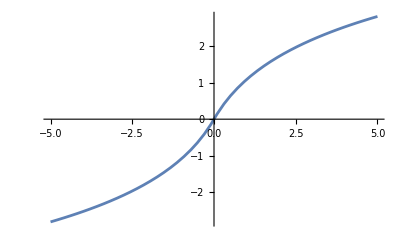

```mathematica
Plot[f[r], {r, -5, 5}]
```

## Naloga 5

Izračunajte naslednje neskončne vsote 
a) 1 + 1 / 2 + 1 / 3 + 1 / 4 + ...  
b) 1 - 1 / 2 + 1 / 3 - 1 / 4 + ...
c) 1 + 1/ 4 + 1 / 9 + 1 / 16 + 1 / 25 + ...

```mathematica
Sum[1/n , {n, 1, Infinity}]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 1/n

```mathematica
Sum[1/n  * (-1)^n, {n, 1, Infinity}]
```

-Log[2]

```mathematica
Sum[1/n^2 , {n, 1, Infinity}]
```

π^2/6

## Naloga 6

Izračunajte posplošena integrala naslednjih funkcij
a) f(x) = ln(x) / (1 - x) na mejah od 0 do 1,
b) f(x) = sin(x) / x na mejah od nič do neskončno,
c) f(x) = 1 / x^(1/2) na mejah od 0 do 1
Ali za izračun potrebujete ukaz Limit?

```mathematica
Integrate[Log[x]/(1-x), {x, 0, 1}]
```

-π^2/6

```mathematica
Integrate[Sin[x]/x, {x, 0, Infinity}]
```

π/2

```mathematica
Integrate[1/x^(1/2), {x, 0, 1}]
```

2